# Having Fun with leaked passwords

Miguel Angel (Mackaber) Bravo Vidales

Almost all Sites use some kind of password

Sometimes when programmers don’t secure their databases correctly, the passwords are hacked

When they’re hacked they get uploaded online

However, sometimes these leaks can help to determine how common is a password

Some people tend to use

Here is a sample of the Database (The original database is Way too big 24Gb uncompressed, so I’m using only the first 50,000 most frequent passwords for this essay)

```mathematica
dataSet =  Import["/Users/mackaber/WSS/Project/Homework/Res/pass_50000.txt","Table","FieldSeparators"-> ":"]
```

{{7C4A8D09CA3762AF61E59520943DC26494F8941B,23174662},{F7C3BC1D808E04732ADF679965CCC34CA7AE3441,7671364},{B1B3773A05C0ED0176787A4F1574FF0075F7521E,3810555},{5BAA61E4C9B93F3F0682250B6CF8331B7EE68FD8,3645804},{3D4F2BF07DC1BE38B20CD6E46949A1071F9D0E3D,3093220},49990,{32C64C6892C674AE8BEB72A239B0CA580A84B406,3402},{4E138A443E5E1663318A91170B2C425AF5FA3CF1,3402},{29C6CFF0E9990A62DD9165B4E659FAC1577F2A77,3402},{4F09C6D977B30BF4762B0481F8487A9DF0948B35,3402},{ADBC4698B1F9B90AA36DB45E59EC184B44B981DA,3402}}
 |  |  |  |

```mathematica
dataset = <|"hash" -> #[[1]],"freq"-> #[[2]]|>& /@dataSet;
dataset//Dataset
```

Dataset[<>]

I found that you can use Hash to get the SHA-1 hash of a String
For example...

```mathematica
Hash["wolfram","SHA","HexString"]
```

a84c43b7866a06a6dd4c9d90e813abbd084f752c

In fact, since hashing a one-way only function, your passwords are stored, since we don’t want to be read by other people, so... how do you know A password is correct?, Easy!, each time you login the hash function applied to the input, then its compared to hash stored in the Database!

Can You Guess the Following password?

```mathematica
Panel[DynamicModule[{pass=password},
Column[{InputField[Dynamic[pass]],
Dynamic[If[Hash[ToString[pass],"SHA","HexString"] === "7c4a8d09ca3762af61e59520943dc26494f8941b",
"Access Granted!",
"Access Denied!"
]]}
]
]]
```

However... This doesn’t mean we can’t crack the password, we know a lot of people in the world actually use weak password which can be found in a dictionary or in list of common words... now... common words, where I have heard that before?

```mathematica
WordList[]//Dataset
```

Dataset[<>]

WordList[] Of course!

If we apply The Hash Function to each one of these words we can have a dictionary to compare our database to!

```mathematica
HashList[wordlist_List] := <|"word" -> #,"hash" -> ToUpperCase@Hash[#,"SHA","HexString"]|>& /@wordlist
HashList[WordList[]]//Dataset
```

Dataset[<>]

Now that we have our dataset with the most common words, the only thing left to do is to see which of the values appear in the leaked database

```mathematica
reverseMap = AssociationMap[Reverse,hashList]
```

<|86F7E437FAA5A7FCE15D1DDCB9EAEAEA377667B8→a,714A417A8A1B4CFC113088608DE9253E99BB0FF5→aah,39172,0FF2D10744FE0E3A4EBFA0FA08B6F061593C0A4D→zygote,E3BCB794E0C0C0A4EFB4FB4757383B09CB4A4F1D→zygotic|>
 |  |  |  |

```mathematica
KeyTake[reverseMap,database//Keys]
```

<|5BAA61E4C9B93F3F0682250B6CF8331B7EE68FD8→password,AB87D24BDC7452E55738DEB5F868E1F16DEA5ACE→monkey,AF8978B1797B72ACFFF9595A5A2A373EC3D9106D→dragon,31F2BFCCE79E11BDE1574CC1C9C8F97A7129A4CB→tinkle,C60266A8ADAD2F8EE67D793B4FD3FD0FFD73CC61→computer,3888,9A498CF634BD6C6CAD2E050E32A4206BFC36B873→supermodel,24F3B4BD2B911B1755AA7E145C91C5E363692826→thinker,531C9E1BFDFF97EF3EDCE06874F68F294F7A1E0F→reboot,089F4E36079EF2742D5EFC7DEF5A5BF5768F6C6E→recycle,0B57C04029DF6E9C49624B3AE761889CF2CB0053→condo|>
 |  |  |  |

But what if the password isn’t one of the most common words?, maybe it is something else like a the name of a company or a country... we can use the entities inside Wolfram

```mathematica
Dataset[KeyTake[AssociationMap[Reverse,HashList[EntityList[EntityClass["DogBreed",All]]//CommonName//ToLowerCase]],database//Keys]]
```

Dataset[<>]

```mathematica
KeyTake[AssociationMap[Reverse,HashList[EntityList[EntityClass["Country","Countries"]]//CommonName//ToLowerCase]],database//Keys]
```

<|1CB5BD5A9E45420321F44C72DA5D90D7F0432FFB→jordan,088E4A2E6F0C20048CD3E53C639C7092BFFB8524→pakistan,AB65D8B9611FB58F4C612F6A5EC239E0E73FD38C→canada,7CE8277C35AC7D51701DECAD652C060741BD7E48→mexico,AE60C4FE057DF2811ECCD9D1ABCF2A7EB5561557→portugal,75B298A477A72F770ADF10F64676986A04BFCD91→australia,23E591E8C36DDA987970603AD0FDD031B7DFF9F9→france,BF3A1BC48EA977DA082723CA040DBA71F55A294E→jamaica,D6F8D358252B59BA5784E89C552AAF2C5E0BA295→georgia,E074138D45B0494966B85AB2E31FA7BA0684F43B→india,CE9415510A40957BD9F4060182F29D08354F64EC→ireland,C705264EC3421BF319168AAD7E8D2E1617BF9487→russia,9AEC35C79B4E91FEFB2A310D33BD736A14C961D8→germany,1187C0B5E46C584C8C9E4F46195716DA2684582C→argentina,FFD4002FF99E67AF4432834C68E58C45F11E3D58→colombia,8F4F9F2DCBAF9BD8EE9E4D1A2CB971A04084157B→israel,F99AECEF3D12E02DCBB6260BBDD35189C89E6E73→indonesia,5009C8E190EE49B3785C61B658C1A999E3510A6E→turkey,6CBFBC47D7DB5FFF87D4397E0C2070B74B104A40→thailand,33E49263A05A4FDA0BFC3BA0906E41FA30C868C5→nigeria,90D014520EED41EFB06DC1736ACB362A613988EE→brazil,B599DE2309E31A21E41394D1614051BB4BE8E2BA→singapore,5A5D7A49980FD29F234A4FEEDE52D85488445D38→jersey,EC285935B46229D40B95438707A7EFB2282F2F02→vietnam,04E211BE7C0964A2686BADEC91C70403A08A703D→panama,405BAA490599055246FFE9CC02FBF9DA11C8A4BA→romania,9AE41083A849FB301183F0CF829D558DDC9802A3→malaysia,01609539A2FBA71B41E3109AB5CB198ADF802DCE→poland,DAEECE5A96FC06A9EF3BA9A676C86ED09C5C22D1→bangladesh,362728D1F1FF951A433CE9EB4CE7A689156F8C85→monaco,1F33462B14F96D3BFB50A70E263555F8BB681EEC→honduras,33B040E1A0C02744176962BA3CEEE4ED561D18AA→senegal,709D9795C258D87D1814B8F0CFB6349FA95C5865→madagascar,ADF9CCE1C94085277DBB04DAAE13D74E754D5011→sweden,0991B566954E8DB56CD5C15C300A50D7BE4632EA→ecuador,5B50F3E60D6ABC8F03A42A3FCD10E6045A1D2D06→greece,A465F978D14C37B6A6EECCB16392CDD2E808D9A4→venezuela,AC49EDA8D7F3F94408E8ECCCCAF38B9675D39982→guatemala,F55ABDA0118D8A7E4481875F8877B70EAD76A340→barbados,3AB9380FA2521F2D0D94FE931B79A1E1EAA91890→china,EA94CB7C6529E9B7F28C3131E7438921DFE7FC5A→japan,27F3950087E4FB51DC972FB2E35BD2753B90F8DB→uganda,0C4FB5956D00091319B39929E084B02E0056BF93→ukraine,93D0305DEC2489BBE1671EB8C1F171343E306A15→bermuda,DD561B8EAA1BA0992E3E681AB46B32FA785BC71D→denmark,B50E1D89E4E7614F32C026A9ADD579A85F439073→norway,6B3312E7518263A1A95FA4391F1CEEC07A72FD07→albania,C34C009102E60D77975598E1F414F8A701C22D0B→chad,1FE80E506149E4B49CA3560003EDD2B8D57E6D9E→austria,06ECD37D683C9AC4AA39442BDCCB68832FB4793E→zimbabwe,672C8C56D3567E46EC4F792B465E82C306C4D544→bahamas,CA78E8D51D058CB43B99450ED44161EB472C8399→afghanistan,BA811CC44CA80CDEABBB54977DCA23DA4FA35F60→lebanon,C8BBEF7DEF40E50600B6D8FB90568BBC28930BB7→cyprus,C073D97DD896FF8DFBF1D4C8AFACE94BEADF7A8E→italy,4E486B4F86520B5C5D4886A04D1F7D84EAA673F6→armenia,AD384E1D704066BB826BDCD01BB716CE403C89E1→tanzania,466E5906DDEC9D69AC9FE8FD81491096D117F4E9→finland,A7AC00C44A7D4D27D0A6A51C400569462B76C643→taiwan,CA1496B3B37AD063A999A234013C15A075672CA7→maldives,B2D0C08C63D15AB5197A239AAE070249799A2509→angola,C1A682EE34908A497082D3049CA604E14E066F62→ethiopia,6143384EEF1AEF4B1879591E381D5475EBB51AF9→moldova,D5213CD33F6BF5450A163D7EBD2A4AB6CEDA8849→martinique,672873F466FDCD9D52C5615854101F3BCBCADC08→bulgaria,3E4A6B39B1B5BCAC2D035657F77ADA78C70C5292→kuwait,068C7358B9010E378BB13B71A55902A5853ED941→nicaragua,6440B4D6A5111D8D290EC12911976C27D8E44843→bolivia,8703707A6445705A79B9C207CA2C604689F2F707→philippines,FBD1930A40DAED6B41FEA5EF669D694D0AE03F6C→guyana,22DDC01D4CD8C9E7DDD532DC595EDD5A81F05918→ghana,B44C2F319F49F0F50033228E57FDFDF2BE8BFCF7→cameroon,0DC5A1887852525756EA9E7B5102078658CEB2F4→uruguay,E9BADBAF44A51D4794E65CECC845C84C19DCE8AD→iceland,D3931759413F555227558A0B18164E9BA77FBA33→montenegro,CB2A884D5CE379A3ACCB985BC6CF77E13A64DDE6→guadeloupe,D3B252686B3F74CC8EA00180E44C23457367BAA7→morocco,1A4F41CC8CC0B32160247E20BF0566C57A86B142→mauritius,9DE97630469E4F8B1D5D12E6B9DAF6F0799309AD→mongolia,EDB4B58B5C91CA9EAA21BCA009CFE777EB3D5D49→belarus,7D5081A572BBFA9186B98F83DA2FED68D6985443→cambodia,D37A8C94EB2827D8323AC89C0893D05902B99148→belize,68C05B14345D7894BB7CC9A7D8E05D97E6B504B2→algeria,6530DFE471612D42CCC15669F9DFCFD2B4DDF73B→paraguay,2673610E6D2962EDDB5936DB325B719F8A397787→kosovo,FD30661443ED479B4394D5513E6CB8AB25D2ABA0→macedonia,8CD5C9947D20D96944EA485BA7534DCF3FE3A3C7→tunisia,51288D140528C2D5C0565891BE70300A9B0E365F→spain,97210F16D145CCD1C7AE1B20FBD2A03B5DA340B0→malawi,C4E7AC099DFD65AF3316D47A7D6BF694A3BAB581→cuba,98616A05E54DD1EBC302E0B1CFB692FD871355B5→croatia,5187540963758B2BFF9E571C8C7411E0931B23A2→slovakia,FF22D85BFD98F1553199BE4D85895ED07B08A411→kenya,BBE956747BD1D5990A3BD561EB86CBBCF6642915→switzerland,F046079030BC699F56909FBF963399315F98C32C→montserrat,8BF85D743952C20C3B310B4742DC81795B7F57C7→dominica,C838F8466B14E3075375A453FABC7F5C0413528E→belgium,342D7473DDA4832C308DB8D7D19BB7DB1B7D445A→gambia,B0194BC50FA9B003283D56739AC314727534D4C2→zambia,C640584834ECA90DD247FBB53E068A55BB420C9E→greenland,F5FE877187A35EC38219024998F94A44EA4C4562→egypt|>

```mathematica
KeyTake[AssociationMap[Reverse,HashList[EntityList[LinguisticAssistant]//CommonName//ToLowerCase]],database//Keys]
```

<||>

```mathematica
list = EntityList[EntityClass["GivenName",{EntityProperty["GivenName","EntityClasses"]->EntityClass["GivenName","UnitedStatesMaleNames"],EntityProperty["GivenName","Number"]->TakeLargest[10000]}]];
KeyTake[AssociationMap[Reverse,HashList[list//CommonName//ToLowerCase]],database//Keys]
```

<||>

```mathematica
WolframAlpha[StringReplace["Leet speak $"],{{"CipherText",1},"ComputableData"}]
```

50|v|37[-]!|\|gee

```mathematica
WolframAlpha["Leet speak something",IncludePods->"Input",AppearanceElements->{"Pods"},TimeConstraint->{20,Automatic,Automatic,Automatic}]
```

WolframAlphaQueryResults

```mathematica
list = StringJoin/@Partition[WordList["CommonWords"],2];
KeyTake[AssociationMap[Reverse,HashList[list]],database//Keys]
```

{aaah,aardvarkaback,abacusabaft,abaloneabandon,abandonedabandonment,abaseabasement,abashabashed,abashmentabate,abatementabattoir,abbeabbess,abbeyabbot,abbreviateabbreviated,abbreviationabdicate,abdicationabdomen,abdominalabduct,abductingabduction,19556,zillionzinc,zinfandelzing,zingerzinnia,zipzipper,zippyzircon,zirconiumzit,zitherzloty,zodiaczodiacal,zombiezonal,zonezoning,zoozoological,zoologistzoology,zoomzoophyte,zoundszucchini,zwiebackzydeco,zygotezygotic}
 |  |  |  |

<||>

$Aborted

```mathematica
dataset
```

{<|hash→7C4A8D09CA3762AF61E59520943DC26494F8941B,freq→23174662|>,<|hash→F7C3BC1D808E04732ADF679965CCC34CA7AE3441,freq→7671364|>,<|hash→B1B3773A05C0ED0176787A4F1574FF0075F7521E,freq→3810555|>,<|hash→5BAA61E4C9B93F3F0682250B6CF8331B7EE68FD8,freq→3645804|>,49993,<|hash→29C6CFF0E9990A62DD9165B4E659FAC1577F2A77,freq→3402|>,<|hash→4F09C6D977B30BF4762B0481F8487A9DF0948B35,freq→3402|>,<|hash→ADBC4698B1F9B90AA36DB45E59EC184B44B981DA,freq→3402|>}
 |  |  |  |

```mathematica
HashList[WordList[]]
```

{<|word→a,hash→86F7E437FAA5A7FCE15D1DDCB9EAEAEA377667B8|>,<|word→aah,hash→714A417A8A1B4CFC113088608DE9253E99BB0FF5|>,<|word→aardvark,hash→FF49ABCA9701606B01B6245D587D26C31B63A433|>,<|word→aback,hash→656AFDA9217251323902917357FABAEB6D475A22|>,39169,<|word→zydeco,hash→B9A25377839FE3FB7F36900DD2CD869BE453BE71|>,<|word→zygote,hash→0FF2D10744FE0E3A4EBFA0FA08B6F061593C0A4D|>,<|word→zygotic,hash→E3BCB794E0C0C0A4EFB4FB4757383B09CB4A4F1D|>}
 |  |  |  |

```mathematica
JoinAcross[HashList[WordList[]],dataset,Key["hash"]]//Dataset
```

Dataset[<>]

```mathematica
Query[All,"admin"]@JoinAcross[HashList[WordList[]],dataset,Key["hash"]]
```

{Missing[KeyAbsent,admin],Missing[KeyAbsent,admin],Missing[KeyAbsent,admin],Missing[KeyAbsent,admin],3891,Missing[KeyAbsent,admin],Missing[KeyAbsent,admin],Missing[KeyAbsent,admin]}
 |  |  |  |

```mathematica
Query[All,{"word","freq"}]@JoinAcross[HashList[{"asdfg"}],dataset,Key["hash"]]
```

{<|word→asdfg,freq→68613|>}

```mathematica
WordCloud[%30[]]
```

$Aborted

```mathematica
WordCloud
```

```mathematica
%30
```

{<|word→password,freq→3645804|>,<|word→monkey,freq→980209|>,<|word→dragon,freq→968625|>,3892,<|word→reboot,freq→3407|>,<|word→recycle,freq→3406|>,<|word→condo,freq→3403|>}
 |  |  |  |

```mathematica
WordCloud[Partition[%38,20]]
```

WordCloud::blnegn: The argument <|word→monkey,freq→980209|> should be non-negative.

WordCloud[{{<|word→password,freq→3645804|>,18,<|word→apple,freq→6|>},193}]
 |  |  |  |

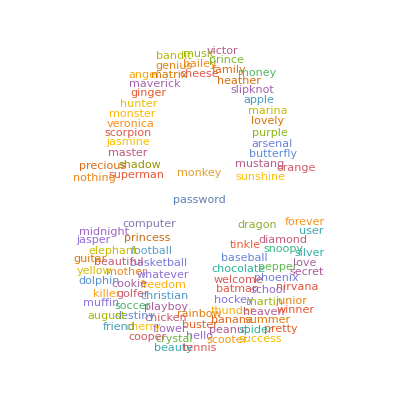

```mathematica
WordCloud[<|#["word"]->ToExpression[#["freq"]]&/@ %38|>,ColorNegate[-Graphics-]]
```

```mathematica
NumberString["1234"]
```

NumberString[1234]

Failure[…]